```mathematica
Solve[√(x^2+1)== 0]
```

{{x→-ⅈ},{x→ⅈ}}

```mathematica
N[π]
```

3.14159

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

```mathematica
N[π, 100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
Plot3D[Sin[x y], {x, -1, 4}, {y, -4, 3}, PlotPoints-> 35]
```

-Graphics3D-

```mathematica
2+3
```

5

```mathematica
Sin[π / 4]
```

1/(√2)

```mathematica
N[Sin[π / 4]]
```

0.707107

```mathematica
N[Sin[π / 4], 50]
```

0.70710678118654752440084436210484903928483593768847

```mathematica
Simplify[Sin[x]^2 + Cos[x]^2]
```

1

```mathematica
Solve[x^2+x== 5, x]
```

{{x→1/2 (-1-√21)},{x→1/2 (-1+√21)}}

```mathematica
Solve[a x^2+b x +c == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Eingabe: N[  Strg+2  1  +  Esc  pi  Esc  Strg+Leertaste  Strg+/  2  Strg+Leertaste   Strg+Leertaste ]
```

```mathematica
N[√(1+π^2/2)]
```

2.43614

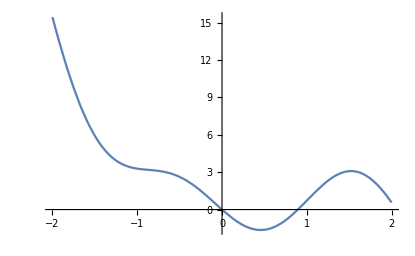

```mathematica
Plot[-x^3+2 x^2-2 Sin[3 x], {x, -2, 2}]
```

```mathematica
Plot3D[Sin[x y], {x, -1, 3}, {y, -2, 2}, PlotPoints-> 30]
```

-Graphics3D-

```mathematica
(* originalImage = DeviceRead["RaspiCam"]; liefert Bild in voller Auflösung, EdgeDetect ist dann sehr langsam *)
```

```mathematica
originalImage = Import["!raspistill -n -w 800 -h 600 -t 1 -o -", "JPG"];
```

```mathematica
ImageDimensions[originalImage]
```

{800,600}

```mathematica
edgeImage = EdgeDetect[originalImage];
```

```mathematica
GraphicsGrid[{{originalImage, edgeImage}}, ImageSize->700]
```

-Graphics-

```mathematica
image = Import["!raspistill -n -w 800 -h 600 -t 1 -o -", "JPG"]
```

-Graphics-